```mathematica
x1 = 0.5;
x2 = 0.88;
ψ50= -3.8;
ψ88= -5.5;

ci=Log[Log[1.-x1]/Log[1.-x2]]/(Log[-ψ50]-Log[-ψ88]);
bi=-ψ50/((-Log[1.-x1])^(1./ci));
k[ψ_]:= (Exp[-(ψ/bi)^ci])
minP = ψ88*3;
maxP = 0.0;
values = Table[{ψ,k[-ψ]}, {ψ, minP, maxP, 0.01}];
θ[ψ_]:=Round[Rescale[ψ, {minP, maxP}, {1, Length@values}]]

values[[θ[-3]]][[2]]
```

0.712376

```mathematica
Table[ψ, {ψ, ψL,ψS, Δψ}]
```

{-4.5,-4.2,-3.9,-3.6,-3.3,-3.,-2.7,-2.4,-2.1,-1.8,-1.5}

```mathematica
MovingAverage[
Table[ψ, {ψ, ψL,ψS, Δψ}],2]
```

{-4.35,-4.05,-3.75,-3.45,-3.15,-2.85,-2.55,-2.25,-1.95,-1.65}

```mathematica
ψS = -1.5;
ψL= -4.5;
ex = NIntegrate[k[-ψ], {ψ, ψL,ψS}]
lin = k[(-ψS -ψL)/2] *(ψS-ψL)
n =10;
Δψ= (ψS-ψL)/n;
trap = Total[Table[k[-ψ]* Δψ, {ψ, MovingAverage[Table[ψ, {ψ, ψL,ψS, Δψ}],2]}]]
trap2 = Total[Table[values[[θ[ψ]]][[2]]* Δψ, {ψ, MovingAverage[Table[ψ, {ψ, ψL,ψS, Δψ}],2]}]]

(lin-ex)/ex*100
(trap-ex)/ex*100
(trap2-ex)/ex*100
```

2.05576

2.13713

2.05638

2.05638

3.95802

0.0299551

0.0299551

```mathematica
ψS = -1.5;
ψL= -4.5;
ψH = 998 * 9.81* 1/10^6;
ex = (1-ψH/(ψS-ψL))*NIntegrate[k[-ψ], {ψ, ψL,ψS}]
n =10;
Δψ= (ψS-ψL)/n;
trap2 = Total[Table[values[[θ[ψ]]][[2]]* (Δψ - ψH/n), {ψ, MovingAverage[Table[ψ, {ψ, ψL,ψS, Δψ}],2]}]]
(trap2-ex)/ex*100
```

2.04905

```mathematica
2.0490506751287496
```

2.04966

```mathematica
SetPrecision[trap2, 16]
```

2.049664469676958

```mathematica
ks[ψ_]:= (Exp[-(ψ/b)^c])
FullSimplify[Series[ks[ψ],{ψ,ψmin,3}]]
```

ⅇ^(-(ψmin/b)^c)-(c ⅇ^(-(ψmin/b)^c) (ψmin/b)^c (ψ-ψmin))/ψmin+(c ⅇ^(-(ψmin/b)^c) (ψmin/b)^c (1+c (-1+(ψmin/b)^c)) (ψ-ψmin)^2)/(2 ψmin^2)+1/(6 ψmin^3)c ⅇ^(-(ψmin/b)^c) (ψmin/b)^c (-2+c (3-c+3 (-1+c) (ψmin/b)^c-c (ψmin/b)^(2 c))) (ψ-ψmin)^3+O[ψ-ψmin]^4

```mathematica
xs[ψ_]:=0.9052696212779617-0.1362156030249193 (ψ-2)-0.058671256021644635 (ψ-2)^2-0.001904062150309273 (ψ-2)^3
```

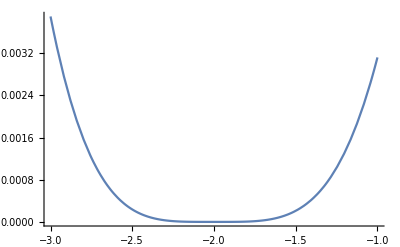

```mathematica
Show[Plot[k[-ψ]-xs[-ψ],{ψ,-3,-1}]]
```

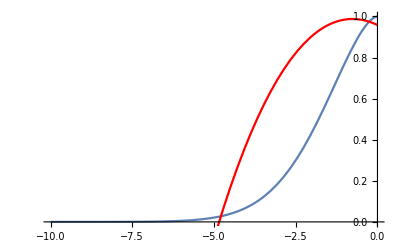

```mathematica
Show[Plot[k[-ψ],{ψ,-10,0}], Plot[xs[-ψ],{ψ,-10,0}, PlotStyle->Red]]
```

```mathematica
Table[ψ, {ψ, ψL,ψS, Δψ}]
```

{-10.5,-8.16667,-5.83333,-3.5}

```mathematica
MovingAverage[
Table[ψ, {ψ, ψL,ψS, Δψ}],2]
```

{-9.33333,-7.,-4.66667}

```mathematica
ψqs = Table[{q,-Chop[FindRoot[k[ψ]== q, {ψ,1}][[1,2]]]
},{q, {0.99,0.950, 0.8, 0.5}}]
```

{{0.99,-0.145116},{0.95,-0.382592},{0.8,-0.917288},{0.5,-1.8}}

```mathematica
si = Table[Normal[Series[k[-ψ],{ψ,ψqs[[s,2]],3}]], {s,1,Length@ψqs}]
```

{0.99+0.115281 (0.145116+ψ)-0.263919 (0.145116+ψ)^2-0.229344 (0.145116+ψ)^3,0.95+0.214143 (0.382592+ψ)-0.166544 (0.382592+ψ)^2-0.0941068 (0.382592+ψ)^3,0.8+0.327209 (0.917288+ψ)-0.054606 (0.917288+ψ)^2-0.0546525 (0.917288+ψ)^3,0.5+0.323727 (1.8+ψ)+0.0435301 (1.8+ψ)^2-0.020667 (1.8+ψ)^3}

```mathematica
ψqss=  ψqs[[All,2]]
```

{-0.145116,-0.382592,-0.917288,-1.8}

```mathematica
(ψqss[[3]]-ψqss[[2]])*0.7
```

-0.374287

```mathematica
(ψqss[[2]]-ψqss[[1]] )* 0.7
```

-0.166233

```mathematica
f3[di_]:= If[Abs[di-ψqss[[4]]]< Abs[(ψqss[[4]]-ψqss[[3]])*0.7], Return[4], If[Abs[di-ψqss[[2]]]<Abs[(ψqss[[2]]-ψqss[[1]] )* 0.7],Return[3], Return[2]]]
```

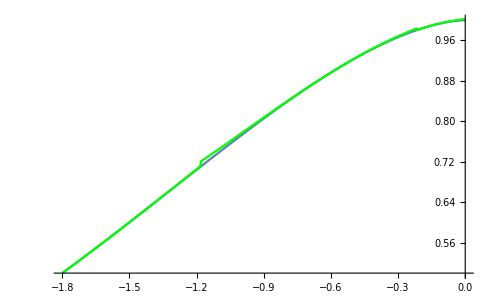

```mathematica
Show[Plot[k[-ψ],{ψ,ψ50,0}],
Plot[si[[f3[ψ]]],{ψ,ψ50,-0}, PlotStyle->Green]]
```

```mathematica
Show[Plot[k[-ψ],{ψ,-10,0}], Plot[xs[-ψ],{ψ,-10,0}, PlotStyle->Red]]
```

-Graphics-

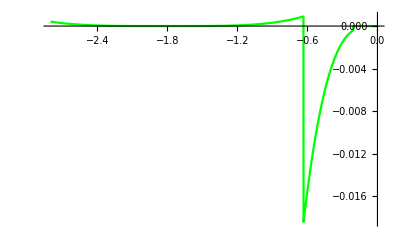

```mathematica
Plot[k[-ψ]-si[[f3[ψ]]],{ψ,-2.8,0}, PlotStyle->Green, PlotRange->All]
```

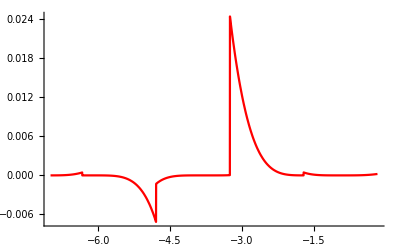

```mathematica
Plot[k[-ψ]-si[[f[ψ]]],{ψ,-7,0}, PlotStyle->Red, PlotRange->All]
```

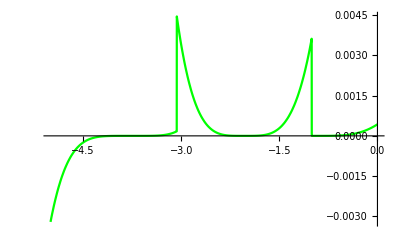

```mathematica
Plot[k[-ψ]-si[[f2[ψ]]],{ψ,-5,-0}, PlotStyle->Green, PlotRange->All]
```

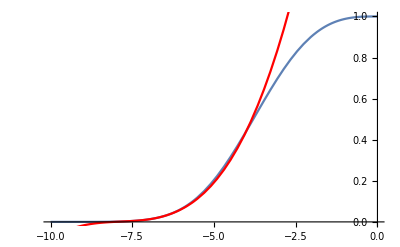

```mathematica
Show[Plot[k[-ψ],{ψ,-10,0}], Plot[s,{ψ,-10,0}, PlotStyle->Red]]
```

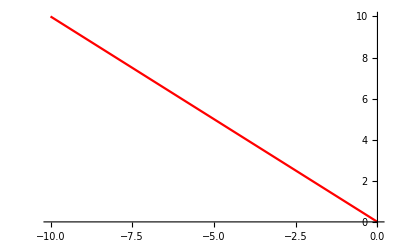

```mathematica
Plot[s/@(-ψ),{ψ,-10,0}, PlotStyle->Red]
```